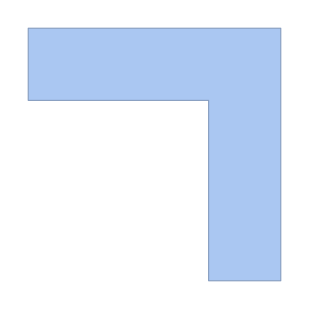

```mathematica
reg=RegionUnion[DiscretizeGraphics[Graphics@Rectangle[{-5,-1},{2,1}]],DiscretizeGraphics[Graphics@Rectangle[{0,-1},{2,-6}]],AspectRatio->1]
```

```mathematica
Manipulate[RegionIntersection[reg,TransformedRegion[TransformedRegion[reg,TranslationTransform[{x,0}]],RotationTransform[alpha,{0,-1}]],PlotRange->{{-6,6},{-6,6}}],{x,0,2},{alpha,0,2Pi}]
```

```mathematica
Manipulate[RegionPlot[{reg,TransformedRegion[TransformedRegion[reg,TranslationTransform[{x,0}]],RotationTransform[-alpha,{0,-1}]]},PlotRange->{{-6,6},{-6,6}}],{x,0,2},{alpha,0,2Pi}]
```

```mathematica
Manipulate[RegionPlot[{reg,TransformedRegion[TransformedRegion[reg,TranslationTransform[{-2Cos[alpha]+1,-1+2Cos[alpha]}]],RotationTransform[-alpha+Pi/4,{0,-1}]]},PlotRange->{{-6,6},{-6,6}}],{alpha,0,Pi/2}]
```

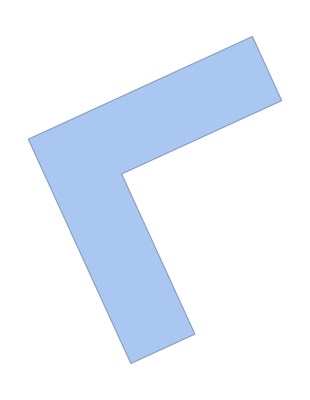

```mathematica
TransformedRegion[reg,RotationTransform[2.]]
```

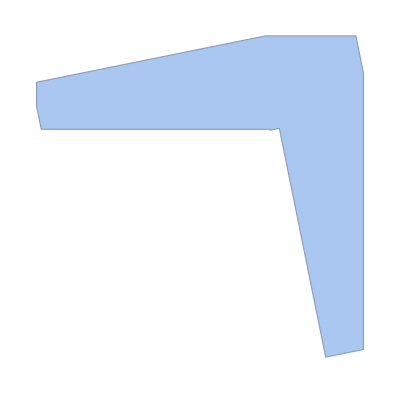

```mathematica
RegionIntersection[reg,TransformedRegion[TransformedRegion[reg,TranslationTransform[{x,0}]],RotationTransform[alpha]]]
```

```mathematica
ListLinePlot[Table[{1.Cos[k alpha],1.Sin[k alpha]}/.k->2.,{alpha,-Pi/4,Pi/4,(Pi/2.)/100.}],AspectRatio->1]
```

```mathematica
regs=Flatten[Table[TransformedRegion[TransformedRegion[reg,TranslationTransform[{0.01Cos[k alpha],0.01Sin[k alpha]}]],RotationTransform[-alpha,{0,-1}]],{alpha,0,Pi/2.,(Pi/2.)/10.},{k,1,9}]];
```

```mathematica
regs
```

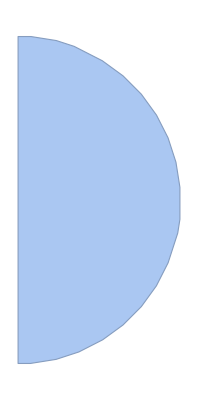

```mathematica
Fold[RegionIntersection,regs]
```

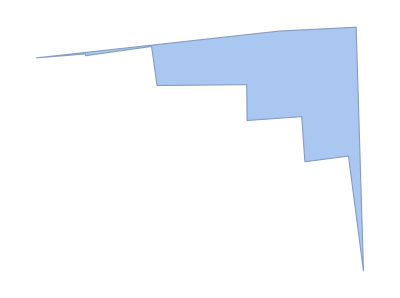

```mathematica
RegionIntersection@@Table[TransformedRegion[TransformedRegion[reg,TranslationTransform[{Cos[10alpha],Sin[10alpha]}]],RotationTransform[0.1*alpha]],{alpha,0,Pi/2.,0.1}]
```

```mathematica
(*Alpha needs to go from 0,Pi/2*)
```

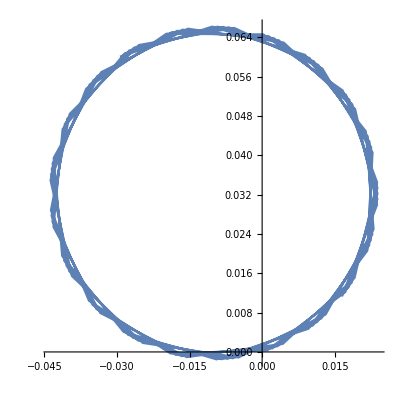

```mathematica
ListLinePlot[Accumulate@Table[{2/100. Cos[k alpha],2/100. Sin[k alpha]}/.alpha->0.6,{k,1,100,1}],AspectRatio->1]
```

```mathematica
ListPlot[Table[{-1Cos[alpha],1},{alpha,0,Pi/2.}]]
```

```mathematica
{-1,1},{1,-1}
```

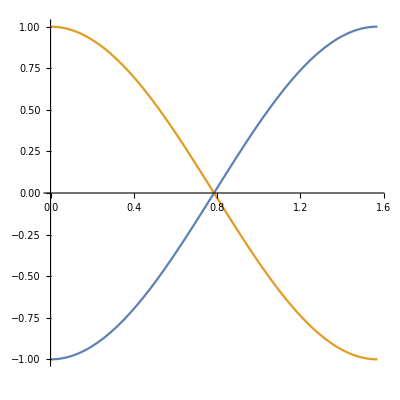

```mathematica
Plot[{-Cos[2 alpha],Cos[2 alpha]},{alpha,0,Pi/2},AspectRatio->1]
```

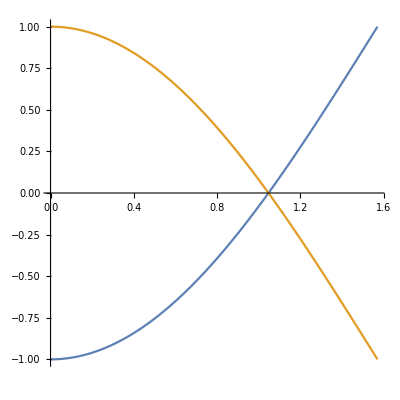

```mathematica
Plot[{-2Cos[alpha]+1,-1+2Cos[alpha]},{alpha,0,Pi/2},AspectRatio->1]
```

```mathematica
Plot[{-Cos[2alpha],Cos[2alpha]},{alpha,0,Pi/2},AspectRatio->1]
```

-Graphics-

```mathematica
regs=Table[TransformedRegion[TransformedRegion[reg,TranslationTransform[{-2Cos[alpha]+1,-1+2Cos[alpha]}]],RotationTransform[-alpha,{0,-1}]],{alpha,0,Pi/2,0.03}];
```

```mathematica
regs=Table[TransformedRegion[TransformedRegion[reg,TranslationTransform[{-Cos[2alpha],Cos[2alpha]}]],RotationTransform[-alpha,{0,-1}]],{alpha,0,Pi/2,0.02}];
```

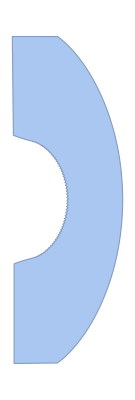

```mathematica
Fold[RegionIntersection,regs]
```

```mathematica
Area[%]
```

8.18185

```mathematica
%/4
```

2.04546

```mathematica
regs=Table[TransformedRegion[TransformedRegion[reg,TranslationTransform[{-0.9Cos[2alpha],0.9Cos[2alpha]}]],RotationTransform[-alpha,{0,-1}]],{alpha,0,Pi/2,0.02}];
```

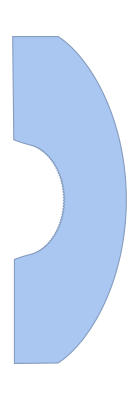

```mathematica
Fold[RegionIntersection,regs]
```

```mathematica
Area[%]
```

8.18533

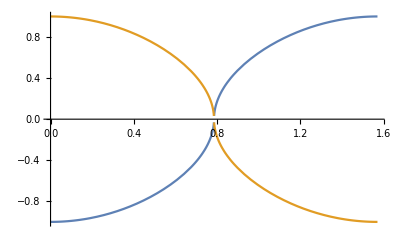

```mathematica
Plot[{-1Sign[Cos[2alpha]]Abs[Cos[2alpha]]^0.5,1Sign[Cos[2alpha]]Abs[Cos[2alpha]]^0.5},{alpha,0,Pi/2}]
```

```mathematica
regs=Table[TransformedRegion[TransformedRegion[reg,TranslationTransform[{-1Sign[Cos[2alpha]]Abs[Cos[2alpha]]^1.1,1Sign[Cos[2alpha]]Abs[Cos[2alpha]]^1.1}]],RotationTransform[-alpha,{0,-1}]],{alpha,0,Pi/2,0.02}];
```

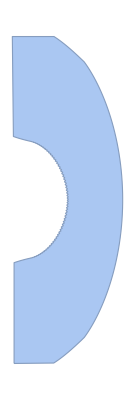

```mathematica
Fold[RegionIntersection,regs]
```

```mathematica
Area[%]
```

8.28222

```mathematica
%/4
```

2.07055

```mathematica
regs=Table[TransformedRegion[TransformedRegion[reg,TranslationTransform[{-1.04Sign[Cos[2alpha]]Abs[Cos[2alpha]]^1.1,1Sign[Cos[2alpha]]Abs[Cos[2alpha]]^1.1}]],RotationTransform[-alpha,{0,-1}]],{alpha,0,Pi/2,0.02}];
```

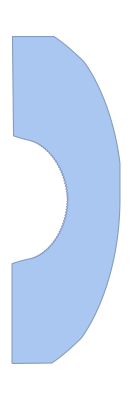

```mathematica
Fold[RegionIntersection,regs]
```

```mathematica
Area[%]
```

8.26161

```mathematica
regs//Length
```

79

```mathematica
FoldList[RegionIntersection,regs[[1;;79]]]
```

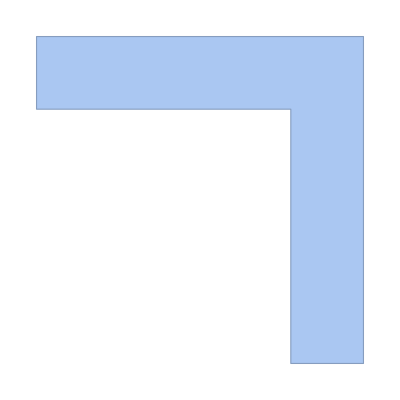

```mathematica
reg=RegionUnion[DiscretizeGraphics[Graphics@Rectangle[{-7,-1},{2,1}]],DiscretizeGraphics[Graphics@Rectangle[{0,-1},{2,-8}]],AspectRatio->1]
```

```mathematica
regs=Table[TransformedRegion[TransformedRegion[reg,TranslationTransform[{-1Sign[Cos[2alpha]]Abs[Cos[2alpha]]^1.1,1Sign[Cos[2alpha]]Abs[Cos[2alpha]]^1.1}]],RotationTransform[-alpha,{0,-1}]],{alpha,0,Pi/2,0.02}];
```

```mathematica
FoldList[RegionIntersection,regs]
```

```mathematica
Manipulate[RegionPlot[{reg,TransformedRegion[TransformedRegion[reg,TranslationTransform[{-1Sign[Cos[2alpha]]Abs[Cos[2alpha]]^1,1Sign[Cos[2alpha]]Abs[Cos[2alpha]]^1}]],RotationTransform[-alpha+Pi/4.,{0,-1}]]},PlotRange->{{-10,10},{-10,10}}],{alpha,0,Pi/2}]
```

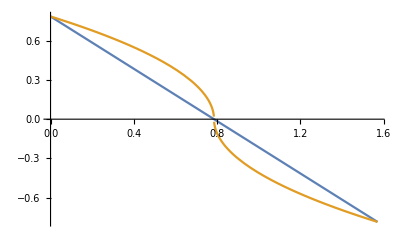

```mathematica
Plot[{-alpha+Pi/4,Sign[-alpha+Pi/4.]Sqrt[Abs[(-alpha+Pi/4.)]*4/Pi]*Pi/4.},{alpha,0,Pi/2}]
```

```mathematica
Manipulate[RegionPlot[{reg,TransformedRegion[TransformedRegion[reg,TranslationTransform[{-1Sign[Cos[2alpha]]Abs[Cos[2alpha]]^1,1Sign[Cos[2alpha]]Abs[Cos[2alpha]]^1}]],RotationTransform[Sign[-alpha+Pi/4.]Sqrt[Abs[(-alpha+Pi/4.)]*4/Pi]*Pi/4.,{0,-1}]]},PlotRange->{{-10,10},{-10,10}}],{alpha,0,Pi/2}]
```

```mathematica
regs=Table[TransformedRegion[TransformedRegion[reg,TranslationTransform[{-1Sign[Cos[2alpha]]Abs[Cos[2alpha]]^1,1Sign[Cos[2alpha]]Abs[Cos[2alpha]]^1}]],RotationTransform[Sign[-alpha+Pi/4.](Abs[(-alpha+Pi/4.)]*4/Pi)^0.6*Pi/4.,{0,-1}]],{alpha,0,Pi/2,0.02}];
```

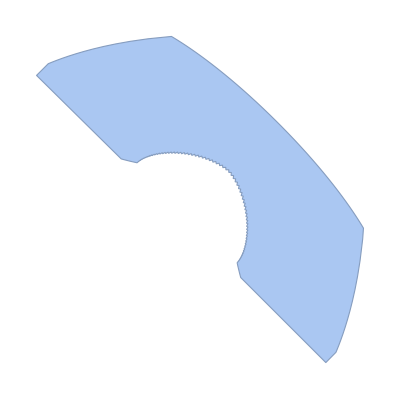

```mathematica
Fold[RegionIntersection,regs]
```

```mathematica
Area[%]
```

8.40544

```mathematica
%/4
```

2.10136

```mathematica
regs=Table[TransformedRegion[TransformedRegion[reg,TranslationTransform[{-1.05Sign[Cos[2alpha]]Abs[Cos[2alpha]]^1,1.05Sign[Cos[2alpha]]Abs[Cos[2alpha]]^1}]],RotationTransform[Sign[-alpha+Pi/4.](Abs[(-alpha+Pi/4.)]*4/Pi)^0.6*Pi/4.,{0,-1}]],{alpha,0,Pi/2,0.02}];
```

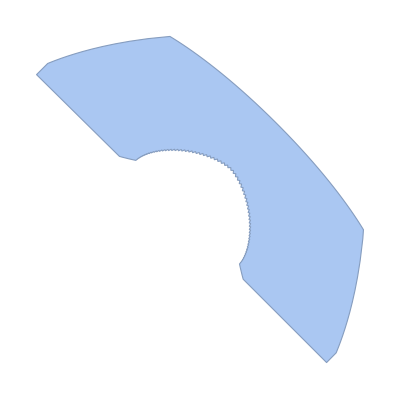

```mathematica
Fold[RegionIntersection,regs]
```

```mathematica
Area[%]
```

8.41839

```mathematica
regs=Table[TransformedRegion[TransformedRegion[reg,TranslationTransform[{-1.01Sign[Cos[2alpha]]Abs[Cos[2alpha]]^1,1.01Sign[Cos[2alpha]]Abs[Cos[2alpha]]^1}]],RotationTransform[Sign[-alpha+Pi/4.](Abs[(-alpha+Pi/4.)]*4/Pi)^0.66*Pi/4.,{0,-1}]],{alpha,0,Pi/2,0.02}];
```

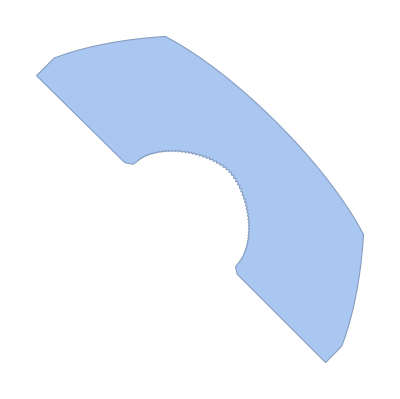

```mathematica
Fold[RegionIntersection,regs]
```

```mathematica
Area[%658]
```

8.45864

```mathematica
regs=Table[TransformedRegion[TransformedRegion[reg,TranslationTransform[{-1.01Sign[Cos[2alpha]]Abs[Cos[2alpha]]^0.98,1.01Sign[Cos[2alpha]]Abs[Cos[2alpha]]^0.98}]],RotationTransform[Sign[-alpha+Pi/4.](Abs[(-alpha+Pi/4.)]*4/Pi)^0.66*Pi/4.,{0,-1}]],{alpha,0,Pi/2,0.02}];
```

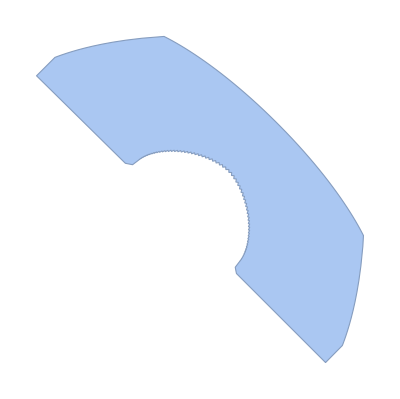

```mathematica
Fold[RegionIntersection,regs]
```

```mathematica
Area[%]
```

8.46654

```mathematica
regs=Table[TransformedRegion[TransformedRegion[reg,TranslationTransform[{-1.01Sign[Cos[2alpha]]Abs[Cos[2alpha]]^0.94,1.01Sign[Cos[2alpha]]Abs[Cos[2alpha]]^0.94}]],RotationTransform[Sign[-alpha+Pi/4.](Abs[(-alpha+Pi/4.)]*4/Pi)^0.66*Pi/4.,{0,-1}]],{alpha,0,Pi/2,0.02}];
```

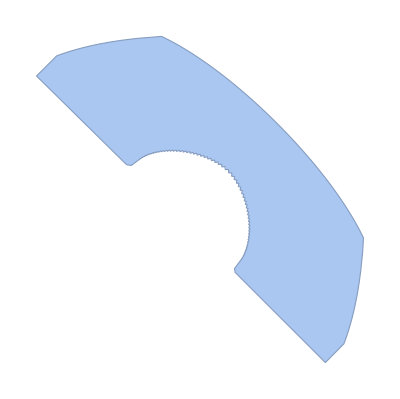

```mathematica
Fold[RegionIntersection,regs]
```

```mathematica
Area[%]
```

8.47997

```mathematica
regs=Table[TransformedRegion[TransformedRegion[reg,TranslationTransform[{-1.01Sign[Cos[2alpha]]Abs[Cos[2alpha]]^0.9,1.01Sign[Cos[2alpha]]Abs[Cos[2alpha]]^0.9}]],RotationTransform[Sign[-alpha+Pi/4.](Abs[(-alpha+Pi/4.)]*4/Pi)^0.66*Pi/4.,{0,-1}]],{alpha,0,Pi/2,0.02}];
```

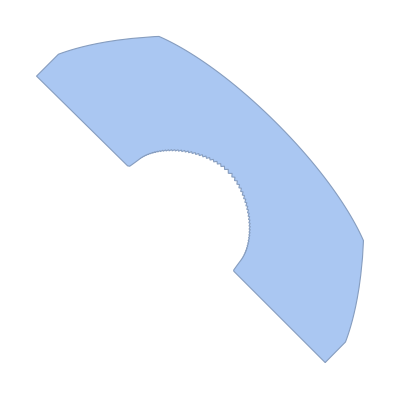

```mathematica
Fold[RegionIntersection,regs]
```

```mathematica
Area[%]
```

8.4896

```mathematica
regs=Table[TransformedRegion[TransformedRegion[reg,TranslationTransform[{-1.01Sign[Cos[2alpha]]Abs[Cos[2alpha]]^0.8,1.01Sign[Cos[2alpha]]Abs[Cos[2alpha]]^0.8}]],RotationTransform[Sign[-alpha+Pi/4.](Abs[(-alpha+Pi/4.)]*4/Pi)^0.66*Pi/4.,{0,-1}]],{alpha,0,Pi/2,0.02}];
```

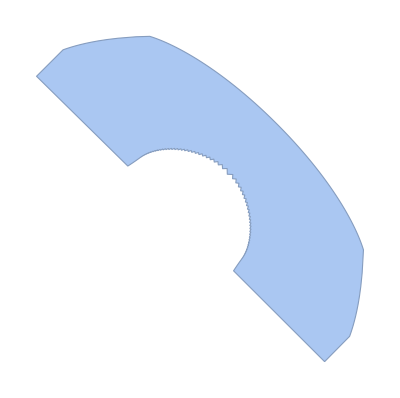

```mathematica
Fold[RegionIntersection,regs]
```

```mathematica
Area[%]
```

8.49304

```mathematica
regs=Table[TransformedRegion[TransformedRegion[reg,TranslationTransform[{-1.01Sign[Cos[2alpha]]Abs[Cos[2alpha]]^0.8,1.01Sign[Cos[2alpha]]Abs[Cos[2alpha]]^0.8}]],RotationTransform[Sign[-alpha+Pi/4.](Abs[(-alpha+Pi/4.)]*4/Pi)^0.63*Pi/4.,{0,-1}]],{alpha,0,Pi/2,0.015}];
```

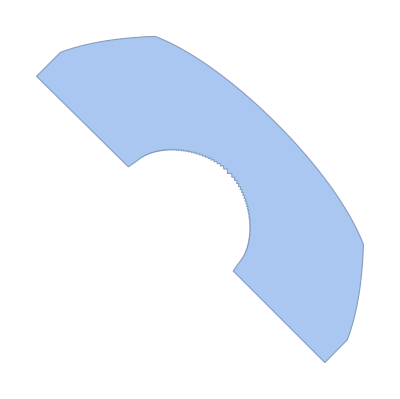

```mathematica
Fold[RegionIntersection,regs]
```

```mathematica
Area[%]
```

8.49835

```mathematica
regs=Table[TransformedRegion[TransformedRegion[reg,TranslationTransform[{-1.01Sign[Cos[2alpha]]Abs[Cos[2alpha]]^0.8,1.01Sign[Cos[2alpha]]Abs[Cos[2alpha]]^0.8}]],RotationTransform[Sign[-alpha+Pi/4.](Abs[(-alpha+Pi/4.)]*4/Pi)^0.6*Pi/4.,{0,-1}]],{alpha,0,Pi/2,0.015}];
```

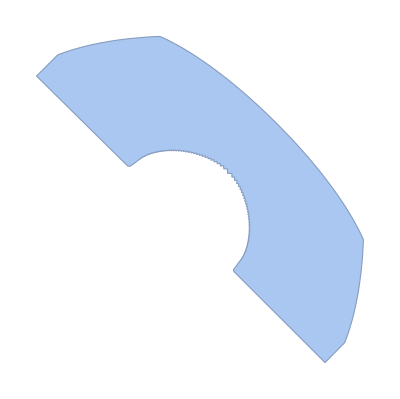

```mathematica
Fold[RegionIntersection,regs]
```

```mathematica
Area[%]
```

8.50305

```mathematica
%/4.
```

2.12576

```mathematica
regs=Table[TransformedRegion[TransformedRegion[reg,TranslationTransform[{-1.2Sign[Cos[2alpha]]Abs[Cos[2alpha]]^0.7,1.2Sign[Cos[2alpha]]Abs[Cos[2alpha]]^0.7}]],RotationTransform[Sign[-alpha+Pi/4.](Abs[(-alpha+Pi/4.)]*4/Pi)^0.53*Pi/4.,{0,-1}]],{alpha,0,Pi/2,0.015}];
```

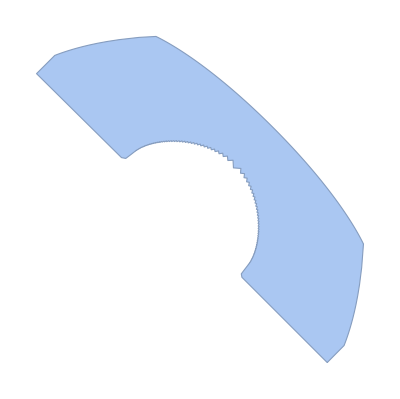

```mathematica
Fold[RegionIntersection,regs]
```

```mathematica
Area[%]
```

8.55506

```mathematica
regs=Table[TransformedRegion[TransformedRegion[reg,TranslationTransform[{-1.225Sign[Cos[2alpha]]Abs[Cos[2alpha]]^0.68,1.225Sign[Cos[2alpha]]Abs[Cos[2alpha]]^0.68}]],RotationTransform[Sign[-alpha+Pi/4.](Abs[(-alpha+Pi/4.)]*4/Pi)^0.53*Pi/4.,{0,-1}]],{alpha,0,Pi/2,0.015}];
```

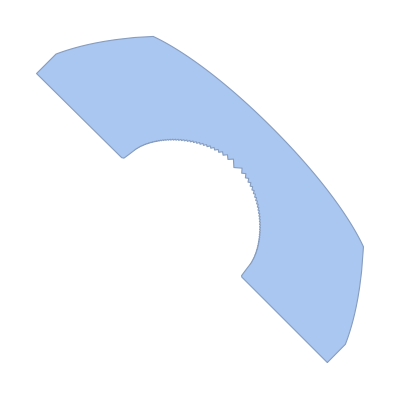

```mathematica
Fold[RegionIntersection,regs]
```

```mathematica
Area[%]
```

8.55843

```mathematica
regs=Table[TransformedRegion[TransformedRegion[reg,TranslationTransform[{-1.225Sign[Cos[2alpha]]Abs[Cos[2alpha]]^0.68,1.225Sign[Cos[2alpha]]Abs[Cos[2alpha]]^0.68}]],RotationTransform[Sign[-alpha+Pi/4.](Abs[(-alpha+Pi/4.)]*4/Pi)^0.52*Pi/4.,{0,-1}]],{alpha,0,Pi/2,0.015}];
```

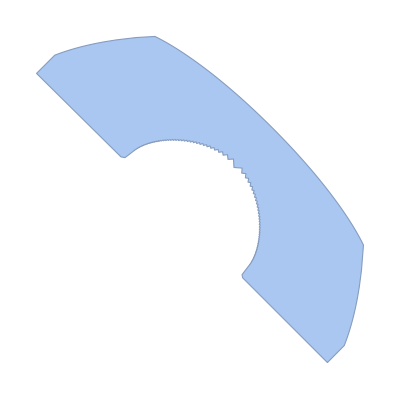

```mathematica
Fold[RegionIntersection,regs]
```

```mathematica
Area[%]
```

8.5583

```mathematica
%/4.
```

2.13957

```mathematica
regs=Table[TransformedRegion[TransformedRegion[reg,TranslationTransform[{-1.225Sign[Cos[2alpha]]Abs[Cos[2alpha]]^0.68,1.225Sign[Cos[2alpha]]Abs[Cos[2alpha]]^0.68}]],RotationTransform[Sign[-alpha+Pi/4.](Abs[(-alpha+Pi/4.)]*4/Pi)^0.52*Pi/4.,{0,-1}]],{alpha,0,Pi/2,0.01}];
```

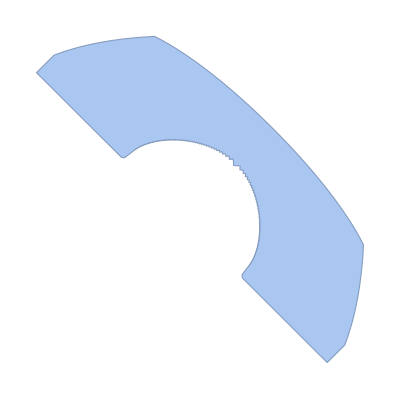

```mathematica
Fold[RegionIntersection,regs]
```

```mathematica
Area[%]
```

8.51918

```mathematica
%/4.
```

2.1298

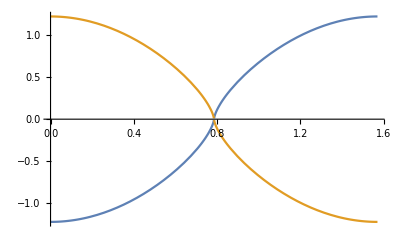

```mathematica
Plot[{-1.225Sign[Cos[2alpha]]Abs[Cos[2alpha]]^0.68,1.225Sign[Cos[2alpha]]Abs[Cos[2alpha]]^0.68},{alpha,0,Pi/2.}]
```

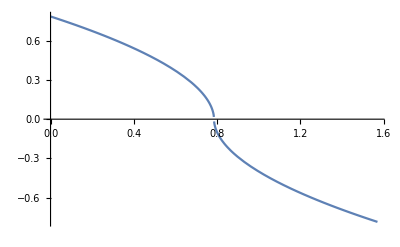

```mathematica
Plot[Sign[-alpha+Pi/4.](Abs[(-alpha+Pi/4.)]*4/Pi)^0.52*Pi/4.,{alpha,0,Pi/2.}]
```

```mathematica
NMaximize
```

```mathematica
results={};Monitor[Table[regs=Table[TransformedRegion[TransformedRegion[reg,TranslationTransform[{-amp Sign[Cos[2alpha]]Abs[Cos[2alpha]]^exp1,amp Sign[Cos[2alpha]]Abs[Cos[2alpha]]^exp1}]],RotationTransform[Sign[-alpha+Pi/4.](Abs[(-alpha+Pi/4.)]*4/Pi)^exp2*Pi/4.,{0,-1}]],{alpha,0,Pi/2,0.015}];AppendTo[results,{amp,exp1,exp2,Area[Fold[RegionIntersection,regs]]}];Export["~/Desktop/results.mx",results],{amp,1.1,1.6,0.1},{exp1,0.55,0.7,0.03},{exp2,0.45,0.6,0.03}];,{amp,exp1,exp2}]
```